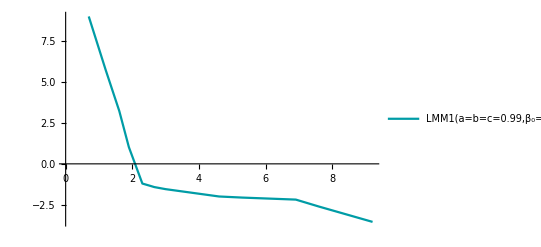

OptionValue::nodef: Graphics 的未知选项 Image.

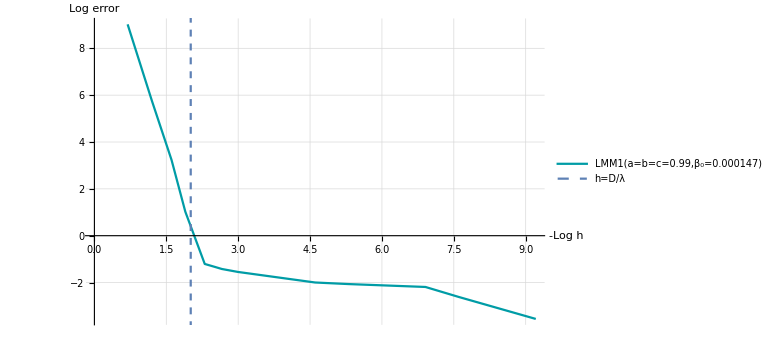

```mathematica
data30={
{-Log[0.5],Log[10,1056206537.6456991434]},
{-Log[0.3],Log[10,540325.1424407196464]},
{-Log[0.2],Log[10,1719.8545534180946106]},
{-Log[0.15],Log[10,10.582451722397580696]},
{-Log[0.1],Log[10,0.062171122450775051504]},
{-Log[0.08],Log[10,0.045763256104804583835]},
{-Log[0.07],Log[10,0.037914372625000303252]},
{-Log[0.05],Log[10,0.0283427508962506014]},
{-Log[0.01],Log[10,0.010043600323003637476]},
{-Log[0.005],Log[10,0.0086111471649350512791]},
{-Log[0.001],Log[10,0.0064762718711746103395]},
{-Log[0.0005],Log[10,0.0024306591138801847407]},
{-Log[0.0001],Log[10,0.00027950622952366277474]}

};
p30=ListLinePlot[data30,Joined->True,PlotStyle->RGBColor[0.,0.61,0.65],PlotLegends->{"LMM1(a=b=c=0.99,β_0=0.000147)"}]
Show[p30,ParametricPlot[{-Log[133.9925851893618/1000],t},{t,-15,30},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],GridLines->Automatic,AxesLabel->{HoldForm[-Log(h)],HoldForm[Log(error)]},Image->Large,LabelStyle->{16,GrayLevel[0]},ImageSize->Large]
```

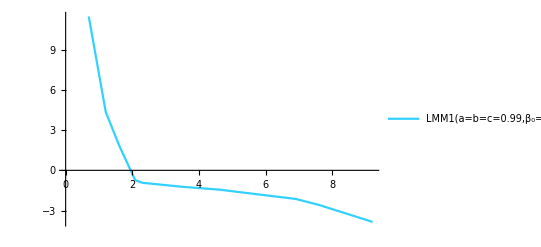

OptionValue::nodef: Graphics 的未知选项 Image.

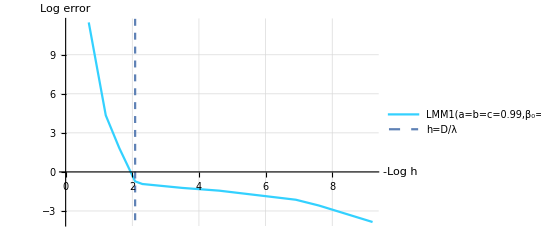

```mathematica
data31={
{-Log[0.5],Log[10,304911965494.82983398]},
{-Log[0.3],Log[10,22278.526503613484238]},
{-Log[0.2],Log[10,68.151964928435077695]},
{-Log[0.1243],Log[10,0.18821811962455492484]},
{-Log[0.1],Log[10,0.11789746917543364457]},
{-Log[0.03],Log[10,0.058844670896385564696]},
{-Log[0.01],Log[10,0.036406921661214314279]},
{-Log[0.001],Log[10,0.0072969640244141542595]},
{-Log[0.0005],Log[10,0.0026144965423918753444]},
{-Log[0.0001],Log[10,0.00014176759726747256707]}

};
p31=ListLinePlot[data31,Joined->True,PlotStyle->RGBColor[0.2,0.82,1.],PlotLegends->{"LMM1(a=b=c=0.99,β_0=-0.001)"}]
Show[p31,ParametricPlot[{-Log[124.2960745/1000],t},{t,-15,30},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],GridLines->Automatic,AxesLabel->{HoldForm[-Log(h)],HoldForm[Log(error)]},Image->Large,LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
|
```

OptionValue::nodef: Graphics 的未知选项 Image.

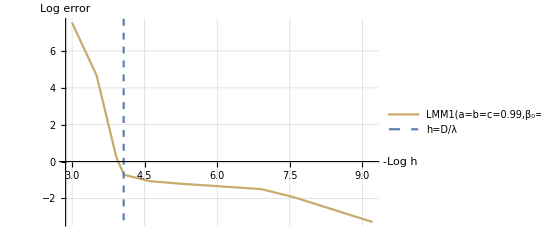

```mathematica
data32={
{-Log[0.05],Log[10,35475228.832459956408]},
{-Log[0.03],Log[10,46766.969346598976699]},
{-Log[0.02],Log[10,1.7796124178862853249]},
{-Log[0.017],Log[10,0.19128868183332214947]},
{-Log[0.01],Log[10,0.086154347092642580286]},
{-Log[0.005],Log[10,0.061507980466285916421]},
{-Log[0.001],Log[10,0.032211572783414466059]},
{-Log[0.0005],Log[10,0.011375446837711189474]},
{-Log[0.0001],Log[10,0.00052605581872877671401]}

};
p32=ListLinePlot[data32,Joined->True,PlotStyle->RGBColor[0.79,0.67,0.43],PlotLegends->{"LMM1(a=b=c=0.99,β_0=-0.1)"}];
Show[p32,ParametricPlot[{-Log[17.154/1000],t},{t,-15,30},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],GridLines->Automatic,AxesLabel->{HoldForm[-Log(h)],HoldForm[Log(error)]},Image->Large,LabelStyle->{12,GrayLevel[0]}]
```

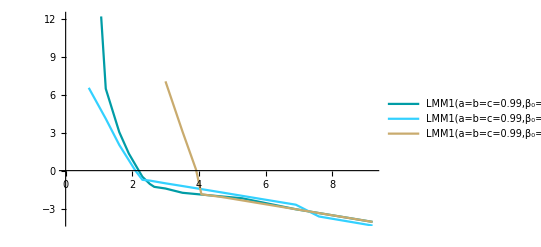

```mathematica
Show[p30,p31,p32]
```